# Lotka-Volterra

## Not everything is working. And cells are sometimes independent from each other...

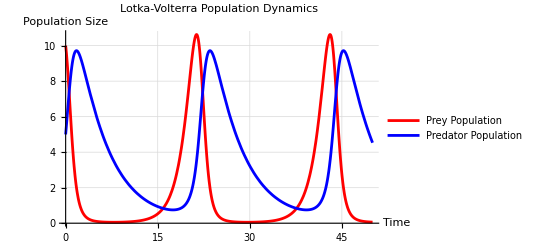
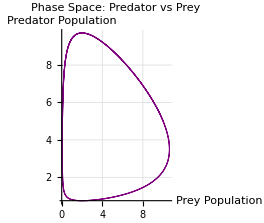
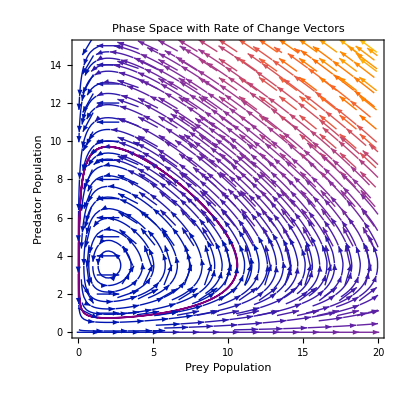
-Graphics- | -Graphics-
-Graphics- |

```mathematica
(*Parameters for the Lotka-Volterra model*)α=0.7;  (*Growth rate of prey*)
β=0.2;  (*Predation rate coefficient*)
γ=0.2;  (*Death rate of predators*)
δ=0.1;  (*Reproduction rate of predators per prey eaten*)

(*Lotka-Volterra differential equations*)
lotkaVolterra={x'[t]==α*x[t]-β*x[t]*y[t],y'[t]==-γ*y[t]+δ*x[t]*y[t]};

(*Initial conditions*)
initialConditions={x[0]==10,(*Initial prey population*)y[0]==5    (*Initial predator population*)};

(*Solve the differential equations*)
solution=NDSolve[Join[lotkaVolterra,initialConditions],{x,y},{t,0,50}];

(*Extract solution functions*)
xSol=x/. solution[[1]];
ySol=y/. solution[[1]];

(*Plot the populations vs time*)
populationPlot=Plot[{xSol[t],ySol[t]},{t,0,50},PlotStyle->{Red,Blue},PlotLegends->{"Prey Population","Predator Population"},AxesLabel->{"Time","Population Size"},PlotLabel->"Lotka-Volterra Population Dynamics",GridLines->Automatic,PlotRange->All];

(*Phase space plot-Prey vs Predator*)
phasePlot=ParametricPlot[{xSol[t],ySol[t]},{t,0,50},AxesLabel->{"Prey Population","Predator Population"},PlotLabel->"Phase Space: Predator vs Prey",GridLines->Automatic,PlotRange->All,PlotStyle->{Thickness[0.003],Purple}];

(*Plot phase space with rate of change vectors*)
vectorFieldPlot=VectorPlot[{α*x-β*x*y,-γ*y+δ*x*y},{x,0,20},{y,0,15},VectorStyle->Red,VectorScale->{Small,Automatic,None},VectorPoints->15,StreamPoints->Fine,PlotLabel->"Vector Field of Rate of Change",AxesLabel->{"Prey Population","Predator Population"}];

(*Combined phase space plot with trajectory*)
combinedPhasePlot=Show[vectorFieldPlot,ParametricPlot[{xSol[t],ySol[t]},{t,0,50},PlotStyle->{Thickness[0.003],Purple}],PlotLabel->"Phase Space with Rate of Change Vectors"];

(*Show the plots side by side*)
Grid[{{populationPlot,phasePlot},{combinedPhasePlot,SpanFromLeft}}]

(*Additionally,create an animation of the phase space trajectory*)
Animate[Show[vectorFieldPlot,ParametricPlot[{xSol[τ],ySol[τ]},{τ,0,t},PlotStyle->{Thickness[0.003],Purple}],Graphics[{Red,PointSize[0.02],Point[{xSol[t],ySol[t]}]}],PlotLabel->"Phase Space Trajectory Animation (t = "<>ToString[N[t]]<>")",PlotRange->{{0,20},{0,15}}],{t,0,50,0.1},AnimationRate->2]
```

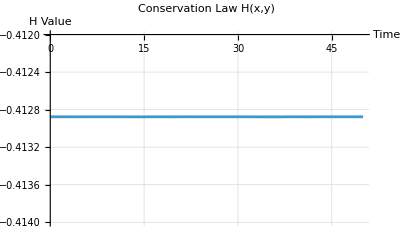

```mathematica
(*Calculate the correct conserved quantity H along the trajectory*)hFunction[x_,y_]:=γ*Log[x]-δ*x+α*Log[y]-β*y;

(*Plot H over time to verify it's constant*)
conservationPlot=Plot[hFunction[xSol[t],ySol[t]],{t,0,50},PlotLabel->"Conservation Law H(x,y)",AxesLabel->{"Time","H Value"},
PlotRange->{-0.414,-0.412},GridLines->Automatic];
conservationPlot
```

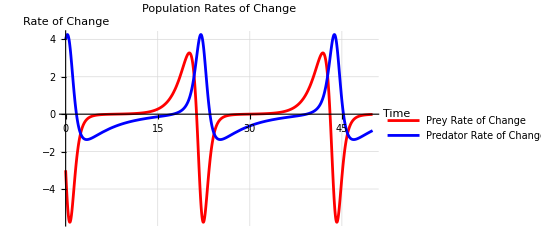
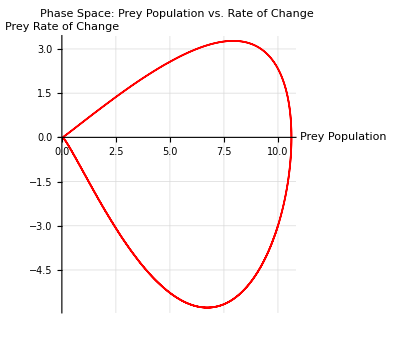
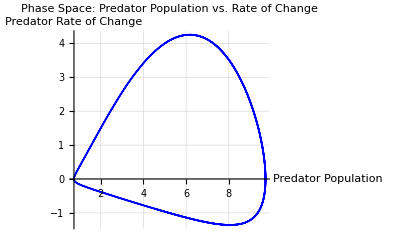
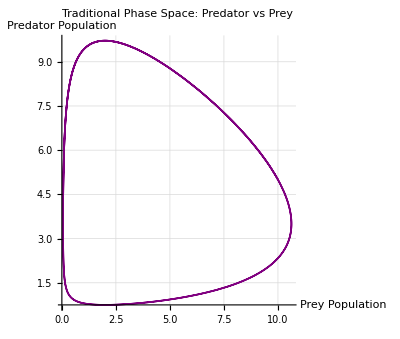
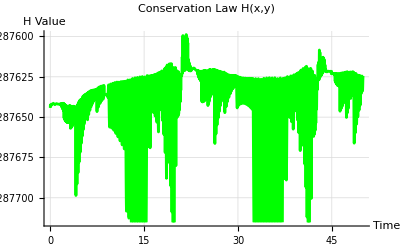
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-

```mathematica
(*Parameters for the Lotka-Volterra model*)α=0.7;  (*Growth rate of prey*)
β=0.2;  (*Predation rate coefficient*)
γ=0.2;  (*Death rate of predators*)
δ=0.1;  (*Reproduction rate of predators per prey eaten*)

(*Lotka-Volterra differential equations*)
lotkaVolterra={x'[t]==α*x[t]-β*x[t]*y[t],y'[t]==-γ*y[t]+δ*x[t]*y[t]};

(*Initial conditions*)
initialConditions={x[0]==10,(*Initial prey population*)y[0]==5    (*Initial predator population*)};

(*Solve the differential equations*)
solution=NDSolve[Join[lotkaVolterra,initialConditions],{x,y},{t,0,50}];

(*Extract solution functions*)
xSol=x/. solution[[1]];
ySol=y/. solution[[1]];

(*Also extract the derivatives-rates of change*)
xDerivative[t_]:=α*xSol[t]-β*xSol[t]*ySol[t];
yDerivative[t_]:=-γ*ySol[t]+δ*xSol[t]*ySol[t];

(*Plot the populations vs time*)
populationPlot=Plot[{xSol[t],ySol[t]},{t,0,50},PlotStyle->{Red,Blue},PlotLegends->{"Prey Population","Predator Population"},AxesLabel->{"Time","Population Size"},PlotLabel->"Lotka-Volterra Population Dynamics",GridLines->Automatic,PlotRange->All];

(*Plot the rates of change vs time*)
rateOfChangePlot=Plot[{xDerivative[t],yDerivative[t]},{t,0,50},PlotStyle->{Red,Blue},PlotLegends->{"Prey Rate of Change","Predator Rate of Change"},AxesLabel->{"Time","Rate of Change"},PlotLabel->"Population Rates of Change",GridLines->Automatic,PlotRange->All];

(*Phase space plot for prey-Population vs.Rate of Change*)
preyPhasePlot=ParametricPlot[{xSol[t],xDerivative[t]},{t,0,50},AxesLabel->{"Prey Population","Prey Rate of Change"},PlotLabel->"Phase Space: Prey Population vs. Rate of Change",GridLines->Automatic,PlotRange->All,PlotStyle->{Thickness[0.003],Red}];

(*Phase space plot for predator-Population vs.Rate of Change*)
predatorPhasePlot=ParametricPlot[{ySol[t],yDerivative[t]},{t,0,50},AxesLabel->{"Predator Population","Predator Rate of Change"},PlotLabel->"Phase Space: Predator Population vs. Rate of Change",GridLines->Automatic,PlotRange->All,PlotStyle->{Thickness[0.003],Blue}];

(*Traditional Phase space plot-Prey vs Predator*)
traditionalPhasePlot=ParametricPlot[{xSol[t],ySol[t]},{t,0,50},AxesLabel->{"Prey Population","Predator Population"},PlotLabel->"Traditional Phase Space: Predator vs Prey",GridLines->Automatic,PlotRange->All,PlotStyle->{Thickness[0.003],Purple}];

(*Calculate the correct conserved quantity*)
conservedH[x_,y_]:=γ*Log[x]-δ*x+α*Log[y]-β*y;

(*Plot the conserved quantity over time*)
conservationPlot=Plot[conservedH[xSol[t],ySol[t]],{t,0,50},PlotLabel->"Conservation Law H(x,y)",AxesLabel->{"Time","H Value"},GridLines->Automatic,PlotStyle->Green];

(*Show the plots in a grid*)
Grid[{{populationPlot,rateOfChangePlot},{preyPhasePlot,predatorPhasePlot},{traditionalPhasePlot,conservationPlot}}]

(*Animation of phase space trajectories*)
Animate[GraphicsGrid[{{(*Prey phase space animation*)Show[ParametricPlot[{xSol[τ],xDerivative[τ]},{τ,0,t},PlotStyle->{Thickness[0.003],Red},AxesLabel->{"Prey Pop.","Rate of Change"},PlotRange->{{0,15},{-3,3}}],Graphics[{Red,PointSize[0.02],Point[{xSol[t],xDerivative[t]}]}]],(*Predator phase space animation*)Show[ParametricPlot[{ySol[τ],yDerivative[τ]},{τ,0,t},PlotStyle->{Thickness[0.003],Blue},AxesLabel->{"Predator Pop.","Rate of Change"},PlotRange->{{0,15},{-1.5,1.5}}],Graphics[{Blue,PointSize[0.02],Point[{ySol[t],yDerivative[t]}]}]]}}],{t,0,50,0.1},AnimationRate->2]
```

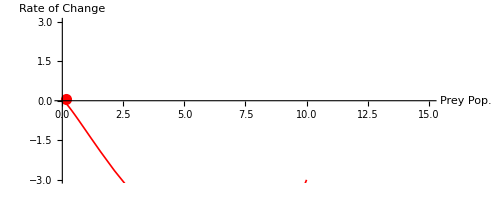

```mathematica
(*Prey phase space animation*)Show[ParametricPlot[{{xSol[τ],xDerivative[τ]}},{τ,0,12},PlotStyle->{Thickness[0.003],Red},AxesLabel->{"Prey Pop.","Rate of Change"},PlotRange->{{0,15},{-3,3}}],Graphics[{Red,PointSize[0.02],Point[{xSol[12],xDerivative[12]}]}]]
```

```mathematica
Animate[(*Prey phase space animation*)Show[ParametricPlot[{{xSol[τ],xDerivative[τ]},{ySol[τ],yDerivative[τ]}},
{τ,0,t},PlotStyle->{
{Thickness[0.003],Blue},
{Thickness[0.003],Red}},AxesLabel->{"Prey Pop.","Rate of Change"},PlotRange->{{0,15},{-6,6}}],
Graphics[
{
{Blue,PointSize[0.02],Point[{xSol[t],xDerivative[t]}]},
{Red,PointSize[0.02],Point[{ySol[t],yDerivative[t]}]}}]
]
,
(*Predator phase space animation*)

{t,0.1,50,0.1},AnimationRate->2]
```

```mathematica
Export["LV.gif",%203]
```

LV.gif

```mathematica
(*Parameters for the Lotka-Volterra model*)α=0.7;  (*Growth rate of prey*)
β=0.2;  (*Predation rate coefficient*)
γ=0.2;  (*Death rate of predators*)
δ=0.1;  (*Reproduction rate of predators per prey eaten*)

(*Original Lotka-Volterra differential equations*)
lotkaVolterra={x'[t]==α*x[t]-β*x[t]*y[t],y'[t]==-γ*y[t]+δ*x[t]*y[t]};

(*Initial conditions*)
initialConditions={x[0]==10,(*Initial prey population*)y[0]==5    (*Initial predator population*)};

(*Solve the differential equations*)
solution=NDSolve[Join[lotkaVolterra,initialConditions],{x,y},{t,0,50}];

(*Extract solution functions*)
xSol=x/. solution[[1]];
ySol=y/. solution[[1]];

(*Calculate the conserved quantity value at t=0*)
conservedH[x_,y_]:=γ*Log[x]-δ*x+α*Log[y]-β*y;
h0=conservedH[xSol[0],ySol[0]];
Print["Initial value of conserved quantity H: ",h0];

(* =====TRANSFORMATION APPROACH 1:LOGARITHMIC VARIABLES=====*)
(*This transforms the system into a form similar to a Hamiltonian system*)

(*Define the transformed variables*)
(*u=ln(x),v=ln(y)*)
(*This transforms the system to:*)
(*u'(t)=α-β*exp(v)*)
(*v'(t)=-γ+δ*exp(u)*)

(*Define transformed conserved quantity*)
transformedH[u_,v_]:=γ*u-δ*Exp[u]+α*v-β*Exp[v];

(*Solve directly for u and v*)
transformedSystem={u'[t]==α-β*Exp[v[t]],v'[t]==-γ+δ*Exp[u[t]],u[0]==Log[10],v[0]==Log[5]};

transformedSolution=NDSolve[transformedSystem,{u,v},{t,0,50}];

uSol=u/. transformedSolution[[1]];
vSol=v/. transformedSolution[[1]];

(*Plot the transformed variables*)
transformedPlot=Plot[{uSol[t],vSol[t]},{t,0,50},PlotStyle->{Red,Blue},PlotLegends->{"ln(x) - Prey","ln(y) - Predator"},AxesLabel->{"Time","Transformed Variables"},PlotLabel->"Transformed Variables: ln(x) and ln(y)",GridLines->Automatic];

(*Verify the conservation law in transformed variables*)
transformedConservationPlot=Plot[transformedH[uSol[t],vSol[t]],{t,0,50},PlotLabel->"Conservation Law in Transformed Variables",AxesLabel->{"Time","H Value"},GridLines->Automatic,PlotStyle->Green];

(*Phase space in transformed variables*)
transformedPhasePlot=ParametricPlot[{uSol[t],vSol[t]},{t,0,50},AxesLabel->{"ln(x) - Prey","ln(y) - Predator"},PlotLabel->"Phase Space in Transformed Variables",GridLines->Automatic,PlotStyle->{Thickness[0.003],Purple}];

(* =====TRANSFORMATION APPROACH 2:ACTION-ANGLE TYPE VARIABLES=====*)
(*We'll attempt to define a variable I that represents the conserved quantity,and an angle θ that parameterizes position along the orbit*)

(*First,find the equilibrium point*)
equilibriumX=γ/δ;
equilibriumY=α/β;
Print["Equilibrium point: (",equilibriumX,", ",equilibriumY,")"];

(*Define a new time variable for orbit parameterization*)
(*We'll parameterize orbits using a transformed time variable*)
(*The period calculation requires numerical integration*)

(*Find the period of oscillation*)
(*First convert to polar coordinates centered at equilibrium*)
rFunctionSquared[t_]:=(xSol[t]-equilibriumX)^2+(ySol[t]-equilibriumY)^2;
angleFunction[t_]:=ArcTan[xSol[t]-equilibriumX,ySol[t]-equilibriumY];

(*Find the period by looking for the first time the angle returns to its initial value*)
(*after a full cycle*)
periodFinder=FindRoot[angleFunction[t]==angleFunction[0]+2π,{t,10,0,50}];
period=t/. periodFinder;
Print["Period of oscillation: ",period];

(*Now define the action-angle variables*)
(*I=H(x,y),the conserved quantity*)
(*θ=normalized time along orbit (0 to 2π)*)
actionFunction[t_]:=conservedH[xSol[t],ySol[t]];
angleFunction[t_]:=2π*Mod[t/period,1];

(*Plot the action-angle variables*)
actionAnglePlot=Plot[{actionFunction[t],angleFunction[t]/(2π)},{t,0,50},PlotStyle->{Red,Blue},PlotLegends->{"I (Action)","θ/(2π) (Angle)"},AxesLabel->{"Time","Action-Angle Variables"},PlotLabel->"Action-Angle Variables",GridLines->Automatic];

(*Phase space in action-angle variables*)
actionAnglePhasePlot=ParametricPlot[{angleFunction[t]/(2π),actionFunction[t]},{t,0,50},AxesLabel->{"θ/(2π) (Angle)","I (Action)"},PlotLabel->"Phase Space in Action-Angle Variables",GridLines->Automatic,PlotStyle->{Thickness[0.003],Purple}];

(* =====VISUALIZATION OF THE REDUCED SYSTEM=====*)
(*With the transformations above,the system reduces to:dI/dt=0 (I remains constant) dθ/dt=ω=2π/period (θ increases linearly with time)*)

(*Reconstruct the original variables from I and θ*)
(*This requires a numerical approach since there's no closed form*)
(*We'll use the parameterized solution as a lookup table*)

(*Create a function that maps from θ to (x,y)*)
(*For a fixed value of I (our initial H)*)
(*We can use the original solution as our map*)

(*Function to parameterize orbit by angle*)
orbitParameterization=Table[{angleFunction[t],xSol[t],ySol[t]},{t,0,period,period/100}];

(*Show everything together*)
GraphicsGrid[{{transformedPlot,transformedPhasePlot},{actionAnglePlot,actionAnglePhasePlot},{transformedConservationPlot,Plot[{xSol[t],ySol[t]},{t,0,50},PlotStyle->{Red,Blue},PlotLegends->{"x(t)","y(t)"},PlotLabel->"Original Variables for Comparison"]}}]
```

Initial value of conserved quantity H: -0.412876

Equilibrium point: (2., 3.5)

FindRoot::reged: The point {50.} is at the edge of the search region {0.,50.} in coordinate 1 and the computed search direction points outside the region.

Period of oscillation: 50.

-Graphics-

```mathematica
(*Parameters for the Lotka-Volterra model*)α=0.7;  (*Growth rate of prey*)
β=0.2;  (*Predation rate coefficient*)
γ=0.2;  (*Death rate of predators*)
δ=0.1;  (*Reproduction rate of predators per prey eaten*)

(*Original Lotka-Volterra differential equations*)
lotkaVolterra={x'[t]==α*x[t]-β*x[t]*y[t],y'[t]==-γ*y[t]+δ*x[t]*y[t]};

(*Initial conditions*)
initialConditions={x[0]==10,(*Initial prey population*)y[0]==5    (*Initial predator population*)};

(*Solve the differential equations*)
solution=NDSolve[Join[lotkaVolterra,initialConditions],{x,y},{t,0,50}];

(*Extract solution functions*)
xSol=x/. solution[[1]];
ySol=y/. solution[[1]];

(*Calculate derivatives-rates of change*)
xDerivative[t_]:=α*xSol[t]-β*xSol[t]*ySol[t];
yDerivative[t_]:=-γ*ySol[t]+δ*xSol[t]*ySol[t];

(*Apply logarithmic transformation*)
uSol[t_]:=Log[xSol[t]];
vSol[t_]:=Log[ySol[t]];

(*Calculate derivatives in transformed space*)
uDerivative[t_]:=α-β*Exp[vSol[t]];
vDerivative[t_]:=-γ+δ*Exp[uSol[t]];

(*Find the equilibrium point*)
equilibriumX=γ/δ;
equilibriumY=α/β;
Print["Equilibrium point: (",equilibriumX,", ",equilibriumY,")"];

(*Find equilibrium in transformed coordinates*)
equilibriumU=Log[equilibriumX];
equilibriumV=Log[equilibriumY];
Print["Equilibrium in transformed coordinates: (",equilibriumU,", ",equilibriumV,")"];

(*Create an animation showing both populations in phase space*)
originalPhaseSpaceAnimation=Animate[Show[(*Prey population vs.rate of change trajectory*)ParametricPlot[{xSol[τ],xDerivative[τ]},{τ,0,t},PlotStyle->{Thickness[0.003],Red},PlotRange->{{0,15},{-3,3}},AxesLabel->{"Population","Rate of Change"},PlotLabel->"Phase Space: Population vs. Rate of Change"],(*Predator population vs.rate of change trajectory*)ParametricPlot[{ySol[τ],yDerivative[τ]},{τ,0,t},PlotStyle->{Thickness[0.003],Blue}],(*Current positions*)Graphics[{Red,PointSize[0.02],Point[{xSol[t],xDerivative[t]}],Blue,PointSize[0.02],Point[{ySol[t],yDerivative[t]}]}],(*Legend*)PlotLegends->{"Prey","Predator"}],{t,0,50,0.1},AnimationRate->2];

(*Create an animation showing both transformed variables in phase space*)
transformedPhaseSpaceAnimation=Animate[Show[(*Transformed prey (u) vs.its rate of change*)ParametricPlot[{uSol[τ],uDerivative[τ]},{τ,0,t},PlotStyle->{Thickness[0.003],Red},PlotRange->{{1,3},{-0.5,0.7}},AxesLabel->{"ln(Population)","Rate of Change"},PlotLabel->"Transformed Phase Space: ln(Population) vs. Rate of Change"],(*Transformed predator (v) vs.its rate of change*)ParametricPlot[{vSol[τ],vDerivative[τ]},{τ,0,t},PlotStyle->{Thickness[0.003],Blue}],(*Current positions*)Graphics[{Red,PointSize[0.02],Point[{uSol[t],uDerivative[t]}],Blue,PointSize[0.02],Point[{vSol[t],vDerivative[t]}]}],(*Equilibrium point*)Graphics[{Black,PointSize[0.015],Point[{equilibriumU,0}],Black,PointSize[0.015],Point[{equilibriumV,0}]}],(*Legend*)PlotLegends->{"ln(Prey)","ln(Predator)"}],{t,0,50,0.1},AnimationRate->2];

(*Create a side-by-side animation comparing original and transformed phase spaces*)
combinedAnimation=Animate[GraphicsRow[{(*Original Phase Space*)Show[ParametricPlot[{xSol[τ],xDerivative[τ]},{τ,0,t},PlotStyle->{Thickness[0.003],Red},PlotRange->{{0,15},{-3,3}},AxesLabel->{"Population","Rate of Change"},PlotLabel->"Original Phase Space"],ParametricPlot[{ySol[τ],yDerivative[τ]},{τ,0,t},PlotStyle->{Thickness[0.003],Blue}],Graphics[{Red,PointSize[0.02],Point[{xSol[t],xDerivative[t]}],Blue,PointSize[0.02],Point[{ySol[t],yDerivative[t]}]}],PlotLegends->{"Prey","Predator"}],(*Transformed Phase Space*)Show[ParametricPlot[{uSol[τ],uDerivative[τ]},{τ,0,t},PlotStyle->{Thickness[0.003],Red},PlotRange->{{1,3},{-0.5,0.7}},AxesLabel->{"ln(Population)","Rate of Change"},PlotLabel->"Transformed Phase Space"],ParametricPlot[{vSol[τ],vDerivative[τ]},{τ,0,t},PlotStyle->{Thickness[0.003],Blue}],Graphics[{Red,PointSize[0.02],Point[{uSol[t],uDerivative[t]}],Blue,PointSize[0.02],Point[{vSol[t],vDerivative[t]}]}],Graphics[{Black,PointSize[0.015],Point[{equilibriumU,0}],Black,PointSize[0.015],Point[{equilibriumV,0}]}],PlotLegends->{"ln(Prey)","ln(Predator)"}]}],{t,0,50,0.1},AnimationRate->2];

(*Another view:Polar coordinates centered at equilibrium*)
(*This shows how the transformation effectively reduces to rotation*)
polarTransformedAnimation=Animate[Module[{rPrey=Sqrt[(xSol[t]-equilibriumX)^2+(xDerivative[t])^2],anglePrey=ArcTan[xSol[t]-equilibriumX,xDerivative[t]],rPred=Sqrt[(ySol[t]-equilibriumY)^2+(yDerivative[t])^2],anglePred=ArcTan[ySol[t]-equilibriumY,yDerivative[t]]},Show[(*Polar trajectory of prey*)ParametricPlot[{(xSol[τ]-equilibriumX),xDerivative[τ]},{τ,0,t},PlotStyle->{Thickness[0.003],Red},PlotRange->{{-5,10},{-3,3}},AspectRatio->1,AxesLabel->{"x - x₀","dx/dt"},PlotLabel->"Centered Phase Space (Equilibrium at Origin)"],(*Polar trajectory of predator*)ParametricPlot[{(ySol[τ]-equilibriumY),yDerivative[τ]},{τ,0,t},PlotStyle->{Thickness[0.003],Blue}],(*Current positions*)Graphics[{Red,PointSize[0.02],Point[{xSol[t]-equilibriumX,xDerivative[t]}],Blue,PointSize[0.02],Point[{ySol[t]-equilibriumY,yDerivative[t]}]}],(*Equilibrium point at origin*)Graphics[{Black,PointSize[0.015],Point[{0,0}]}],(*Legend*)PlotLegends->{"Prey","Predator"}]],{t,0,50,0.1},AnimationRate->2];

(*Return different animations to explore*)
{combinedAnimation,polarTransformedAnimation}
```

SetDelayed::write: Tag InterpolatingFunction in InterpolatingFunction[{{0.,50.}},{5,7,1,{279},{4},0,0,0,0,Automatic,{},{},False},{{0.,«49»,«229»}},«1»,{Automatic}][t_] is Protected.

Equilibrium point: (2., 3.5)

Equilibrium in transformed coordinates: (0.693147, 1.25276)

{,}

```mathematica
(*Parameters for the Lotka-Volterra model*)
α=0.7;  (*Growth rate of prey*)
β=0.2;  (*Predation rate coefficient*)
γ=0.2;  (*Death rate of predators*)
δ=0.1;  (*Reproduction rate of predators per prey eaten*)

(*Original Lotka-Volterra differential equations*)
lotkaVolterra={x'[t]==α*x[t]-β*x[t]*y[t],y'[t]==-γ*y[t]+δ*x[t]*y[t]};

(*Initial conditions*)
initialConditions={x[0]==10,(*Initial prey population*)y[0]==5    (*Initial predator population*)};

(*Solve the differential equations*)
solution=NDSolve[Join[lotkaVolterra,initialConditions],{x,y},{t,0,50}];

(*Extract solution functions*)
xSol=x/. solution[[1]];
ySol=y/. solution[[1]];

(*Find the equilibrium point-center of the orbit*)
equilibriumX=γ/δ;
equilibriumY=α/β;
Print["Equilibrium point: (",equilibriumX,", ",equilibriumY,")"];

(*Shift coordinates to have the equilibrium at the origin*)
shiftedX[t_]:=xSol[t]-equilibriumX;
shiftedY[t_]:=ySol[t]-equilibriumY;

(*Convert to polar coordinates centered at equilibrium*)
radius[t_]:=Sqrt[shiftedX[t]^2+shiftedY[t]^2];
(*Use ArcTan with two arguments to get correct quadrant*)
theta[t_]:=ArcTan[shiftedX[t],shiftedY[t]];

(*Unwrap the angle to avoid jumps from-π to π*)
unwrappedTheta[0.]=theta[0];



For[i=1,i<=1000,i++,t=50.0*i/1000;
tPrev=50.0*(i-1)/1000;
diff=theta[t]-theta[tPrev];
(*Check for wraparound and adjust*)If[diff>π,diff=diff-2π];
If[diff<-π,diff=diff+2π];
unwrappedTheta[t]=unwrappedTheta[tPrev]+diff;];

(*Find the period of oscillation by finding when we make a full rotation*)
(*Get sample times for calculating period*)
sampleTimes=Table[t,{t,0,50,0.05}];
(*Get theta values at those times*)
thetaValues=Map[theta,sampleTimes];
(*Detect when we cross from negative to positive angle (approx.full rotation)*)
crossings={};
For[i=2,i<=Length[thetaValues],i++,If[thetaValues[[i-1]]<-2.5&&thetaValues[[i]]>2.5,AppendTo[crossings,sampleTimes[[i]]]]];
(*Calculate periods as differences between crossings*)
periods=Table[crossings[[i+1]]-crossings[[i]],{i,1,Length[crossings]-1}];
averagePeriod=Mean[periods];
Print["Average period: ",averagePeriod];

(*Track full rotations for plotting*)
rotations=Table[0,{t,0,50,0.05}];
rotation=0;
For[i=2,i<=Length[thetaValues],i++,(*When we cross from near-π to near π,increment rotation counter*)If[thetaValues[[i-1]]<-2.5&&thetaValues[[i]]>2.5,rotation++];
rotations[[i]]=rotation;];

(*Create table of times and rotations*)
timeRotationData=Table[{sampleTimes[[i]],rotations[[i]]},{i,1,Length[sampleTimes]}];

(*Create table of times and unwrapped angles*)
timeAngleData=Table[{t,unwrappedTheta[t]},{t,0,50,0.05}];

(*Plot the radius over time*)
radiusPlot=ListPlot[Table[{t,radius[t]},{t,0,50,0.1}],Joined->True,PlotStyle->Red,AxesLabel->{"Time","Radius"},PlotLabel->"Radius from Equilibrium Point",GridLines->Automatic];

(*Plot the angle over time*)
anglePlot=ListPlot[Table[{t,theta[t]},{t,0,50,0.05}],Joined->True,PlotStyle->Blue,AxesLabel->{"Time","Angle (radians)"},PlotLabel->"Angular Motion Over Time",GridLines->Automatic,PlotRange->All];

(*Plot the unwrapped angle over time*)
unwrappedAnglePlot=ListPlot[timeAngleData,Joined->True,PlotStyle->Green,AxesLabel->{"Time","Unwrapped Angle (radians)"},PlotLabel->"Unwrapped Angular Motion Over Time",GridLines->Automatic,PlotRange->All];

(*Plot the rotation count over time*)
rotationPlot=ListPlot[timeRotationData,Joined->True,PlotStyle->Purple,AxesLabel->{"Time","Complete Rotations"},PlotLabel->"Number of Complete Rotations Over Time",GridLines->Automatic];

(*Plot angular velocity over time*)
(*Calculate numerical derivative of theta*)
angularVelocities={};
For[i=2,i<=Length[timeAngleData],i++,dt=timeAngleData[[i,1]]-timeAngleData[[i-1,1]];
dTheta=timeAngleData[[i,2]]-timeAngleData[[i-1,2]];
angularVelocity=dTheta/dt;
AppendTo[angularVelocities,{timeAngleData[[i,1]],angularVelocity}];];

angularVelocityPlot=ListPlot[angularVelocities,Joined->True,PlotStyle->Orange,AxesLabel->{"Time","Angular Velocity (rad/s)"},PlotLabel->"Angular Velocity Over Time",GridLines->Automatic];

(*Create polar plot to visualize motion in polar coordinates*)
polarPlot=PolarPlot[Evaluate[Table[radius[t],{t,0,50,0.5}]],{t,0,2π},PolarGridLines->Automatic,PlotStyle->Blue,PlotLabel->"Trajectory in Polar Coordinates"];

(*Animation showing angular motion in polar coordinates*)
frames=Table[Show[PolarPlot[radius[t],{θ,0,2π},PolarGridLines->Automatic,PlotRange->{{-10,10},{-10,10}}],Graphics[{Red,PointSize[0.03],Point[{radius[t]*Cos[theta[t]],radius[t]*Sin[theta[t]]}],Arrow[{{0,0},{radius[t]*Cos[theta[t]],radius[t]*Sin[theta[t]]}}]}],PlotLabel->"Angular Motion Animation (t = "<>ToString[N[t]]<>")"],{t,0,50,1}];

(*Display the graphs in a grid*)
Grid[{{anglePlot,unwrappedAnglePlot},{rotationPlot,angularVelocityPlot},{radiusPlot,polarPlot}}]

(*Create an animation showing the angular motion*)
Export["angular_motion.gif",frames,"AnimationRepetitions"->Infinity,"DisplayDurations"->0.1];

(*Animation for phase space with angle visualization*)
phaseFrames=Table[Show[(*Standard phase space*)ParametricPlot[{xSol[τ],ySol[τ]},{τ,0,50},PlotStyle->{Opacity[0.3],Gray},AxesLabel->{"Prey Population","Predator Population"},PlotRange->{{0,15},{0,10}}],(*Current position*)Graphics[{Red,PointSize[0.02],Point[{xSol[t],ySol[t]}]}],(*Arrow from equilibrium to current position*)Graphics[{Blue,Arrow[{{equilibriumX,equilibriumY},{xSol[t],ySol[t]}}]}],(*Angle representation*)Graphics[{Green,Thickness[0.003],Circle[{equilibriumX,equilibriumY},0.5,{0,theta[t]}]}],(*Equilibrium point*)Graphics[{Black,PointSize[0.02],Point[{equilibriumX,equilibriumY}]}],PlotLabel->"Phase Space with Angular Motion (t = "<>ToString[N[t]]<>", θ = "<>ToString[N[theta[t]]]<>")"],{t,0,50,1}];

Export["phase_angle.gif",phaseFrames,"AnimationRepetitions"->Infinity,"DisplayDurations"->0.1];
```

Equilibrium point: (2., 3.5)

Average period: Mean[{}]

-Graphics-

```mathematica
theta[3]
```

2.01375[3]

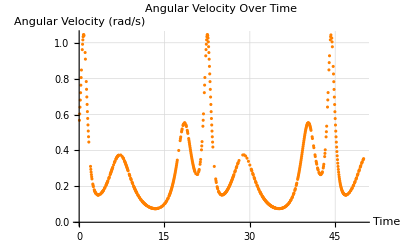

```mathematica
angularVelocities={};
For[i=2,i<=Length[timeAngleData],i++,dt=timeAngleData[[i,1]]-timeAngleData[[i-1,1]];
dTheta=timeAngleData[[i,2]]-timeAngleData[[i-1,2]];
angularVelocity=dTheta/dt;
AppendTo[angularVelocities,
{timeAngleData[[i,1]],angularVelocity}];];



angularVelocityPlot=ListPlot[angularVelocities,
(*Joined->True,*)
PlotStyle->Orange,AxesLabel->{"Time","Angular Velocity (rad/s)"},PlotLabel->"Angular Velocity Over Time",GridLines->Automatic]
```

```mathematica
(*Unwrap the angle to avoid jumps from-π to π*)
unwrappedTheta[0.]=theta[0];
For[i=1,i<=10,i++,
t=50.0*i/1000;
tPrev=50.0*(i-1)/1000;
(*Print[tPrev,"  ", unwrappedTheta[tPrev]];*)
diff=theta[t]-theta[tPrev];
(*Check for wraparound and adjust*)
If[diff>π,diff=diff-2π];
If[diff<-π,diff=diff+2π];
unwrappedTheta[t]=unwrappedTheta[tPrev]+diff;
];
```

```mathematica
50.0*0/1000
```

0.

```mathematica
unwrappedAnglePlot=ListPlot[timeAngleData,Joined->True,PlotStyle->Green,AxesLabel->{"Time","Unwrapped Angle (radians)"},PlotLabel->"Unwrapped Angular Motion Over Time",GridLines->Automatic,PlotRange->All];
unwrappedAnglePlot
```

Equilibrium point: (2., 3.5)

Initial value of action variable I = -0.412876

FindRoot::eqlist: In the first argument ArcTan[«1»]==0.185348&&t>5 only some of the components are equations.

ReplaceAll::reps: {FindRoot[angle[t]==angle[0]&&t>5,{t,10,5,20}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::eqlist: In the first argument ArcTan[«1»]==0.185348&&t>5 only some of the components are equations.

ReplaceAll::reps: {FindRoot[angle[t]==angle[0]&&t>5,{t,10,5,20}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::eqlist: In the first argument ArcTan[«1»]==0.185348&&t>5 only some of the components are equations.

ReplaceAll::reps: {FindRoot[angle[t]==angle[0]&&t>5,{t,10,5,20}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Period of oscillation for this orbit: t/.FindRoot[angle[t]==angle[0]&&t>5,{t,10,5,20}]

FindRoot::eqlist: In the first argument ArcTan[«1»]==0.185348&&t>5 only some of the components are equations.

ReplaceAll::reps: {FindRoot[angle[t]==angle[0]&&t>5,{t,10,5,20}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::eqlist: In the first argument ArcTan[«1»]==0.185348&&t>5 only some of the components are equations.

ReplaceAll::reps: {FindRoot[angle[t]==angle[0]&&t>5,{t,10,5,20}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::eqlist: In the first argument ArcTan[«1»]==0.185348&&t>5 only some of the components are equations.

ReplaceAll::reps: {FindRoot[angle[t]==angle[0]&&t>5,{t,10,5,20}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Angular frequency ω = (2 π)/(t/.FindRoot[angle[t]==angle[0]&&t>5,{t,10,5,20}])

FindRoot::eqlist: In the first argument ArcTan[«1»]==0.185348&&t>5 only some of the components are equations.

ReplaceAll::reps: {FindRoot[angle[t]==angle[0]&&t>5,{t,10,5,20}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::eqlist: In the first argument ArcTan[«1»]==0.185348&&t>5 only some of the components are equations.

ReplaceAll::reps: {FindRoot[angle[t]==angle[0]&&t>5,{t,10,5,20}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::eqlist: In the first argument ArcTan[«1»]==0.185348&&t>5 only some of the components are equations.

General::stop: Further output of FindRoot::eqlist will be suppressed during this calculation.

ReplaceAll::reps: {FindRoot[angle[t]==angle[0]&&t>5,{t,10,5,20}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

Part::partd: Part specification RecursionLimit⟦4⟧ is longer than depth of object.

Part::partd: Part specification RecursionLimit⟦2⟧ is longer than depth of object.

Interpolation::innd: First argument in TerminatedEvaluation[{{RecursionLimit⟦4⟧,RecursionLimit⟦2⟧}}] does not contain a list of data and coordinates.

Part::partd: Part specification RecursionLimit⟦4⟧ is longer than depth of object.

Part::partd: Part specification RecursionLimit⟦3⟧ is longer than depth of object.

Interpolation::innd: First argument in TerminatedEvaluation[{{RecursionLimit⟦4⟧,RecursionLimit⟦3⟧}}] does not contain a list of data and coordinates.

(x,y) values for different angles (fixed action I = -0.412876)

{{Interpolation[TerminatedEvaluation[{{RecursionLimit⟦4⟧,RecursionLimit⟦2⟧}}]][0],Interpolation[TerminatedEvaluation[{{RecursionLimit⟦4⟧,RecursionLimit⟦3⟧}}]][0]},{Interpolation[TerminatedEvaluation[{{RecursionLimit⟦4⟧,RecursionLimit⟦2⟧}}]][π/4],Interpolation[TerminatedEvaluation[{{RecursionLimit⟦4⟧,RecursionLimit⟦3⟧}}]][π/4]},{Interpolation[TerminatedEvaluation[{{RecursionLimit⟦4⟧,RecursionLimit⟦2⟧}}]][π/2],Interpolation[TerminatedEvaluation[{{RecursionLimit⟦4⟧,RecursionLimit⟦3⟧}}]][π/2]},{Interpolation[TerminatedEvaluation[{{RecursionLimit⟦4⟧,RecursionLimit⟦2⟧}}]][(3 π)/4],Interpolation[TerminatedEvaluation[{{RecursionLimit⟦4⟧,RecursionLimit⟦3⟧}}]][(3 π)/4]},{Interpolation[TerminatedEvaluation[{{RecursionLimit⟦4⟧,RecursionLimit⟦2⟧}}]][π],Interpolation[TerminatedEvaluation[{{RecursionLimit⟦4⟧,RecursionLimit⟦3⟧}}]][π]},{Interpolation[TerminatedEvaluation[{{RecursionLimit⟦4⟧,RecursionLimit⟦2⟧}}]][(5 π)/4],Interpolation[TerminatedEvaluation[{{RecursionLimit⟦4⟧,RecursionLimit⟦3⟧}}]][(5 π)/4]},{Interpolation[TerminatedEvaluation[{{RecursionLimit⟦4⟧,RecursionLimit⟦2⟧}}]][(3 π)/2],Interpolation[TerminatedEvaluation[{{RecursionLimit⟦4⟧,RecursionLimit⟦3⟧}}]][(3 π)/2]},{Interpolation[TerminatedEvaluation[{{RecursionLimit⟦4⟧,RecursionLimit⟦2⟧}}]][(7 π)/4],Interpolation[TerminatedEvaluation[{{RecursionLimit⟦4⟧,RecursionLimit⟦3⟧}}]][(7 π)/4]},{Interpolation[TerminatedEvaluation[{{RecursionLimit⟦4⟧,RecursionLimit⟦2⟧}}]][2 π],Interpolation[TerminatedEvaluation[{{RecursionLimit⟦4⟧,RecursionLimit⟦3⟧}}]][2 π]}}

FindRoot::eqlist: In the first argument ArcTan[«1»]==0.185348&&t>5 only some of the components are equations.

ReplaceAll::reps: {FindRoot[angle[t]==angle[0]&&t>5,{t,10,5,20}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::eqlist: In the first argument ArcTan[«1»]==0.185348&&t>5 only some of the components are equations.

ReplaceAll::reps: {FindRoot[angle[t]==angle[0]&&t>5,{t,10,5,20}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::eqlist: In the first argument ArcTan[«1»]==0.185348&&t>5 only some of the components are equations.

General::stop: Further output of FindRoot::eqlist will be suppressed during this calculation.

ReplaceAll::reps: {FindRoot[angle[t]==angle[0]&&t>5,{t,10,5,20}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

Set::shape: Lists {x,y} and RecursionLimit are not the same shape.

Table::nliter: Non-list iterator {x,y}=RecursionLimit at position 2 does not evaluate to a real numeric value.

(I,θ) values for points on the orbit:

TerminatedEvaluation[Table[{IFromXY[x,y],θFromXY[x,y]},{x,y}=RecursionLimit]]

FindRoot::eqlist: In the first argument ArcTan[«1»]==0.185348&&t>5 only some of the components are equations.

ReplaceAll::reps: {FindRoot[angle[t]==angle[0]&&t>5,{t,10,5,20}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::eqlist: In the first argument ArcTan[«1»]==0.185348&&t>5 only some of the components are equations.

ReplaceAll::reps: {FindRoot[angle[t]==angle[0]&&t>5,{t,10,5,20}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::eqlist: In the first argument ArcTan[«1»]==0.185348&&t>5 only some of the components are equations.

General::stop: Further output of FindRoot::eqlist will be suppressed during this calculation.

ReplaceAll::reps: {FindRoot[angle[t]==angle[0]&&t>5,{t,10,5,20}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

FindRoot::eqlist: In the first argument ArcTan[«1»]==0.185348&&t>5 only some of the components are equations.

ReplaceAll::reps: {FindRoot[angle[t]==angle[0]&&t>5,{t,10,5,20}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::eqlist: In the first argument ArcTan[«1»]==0.185348&&t>5 only some of the components are equations.

ReplaceAll::reps: {FindRoot[angle[t]==angle[0]&&t>5,{t,10,5,20}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::eqlist: In the first argument ArcTan[«1»]==0.185348&&t>5 only some of the components are equations.

General::stop: Further output of FindRoot::eqlist will be suppressed during this calculation.

ReplaceAll::reps: {FindRoot[angle[t]==angle[0]&&t>5,{t,10,5,20}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

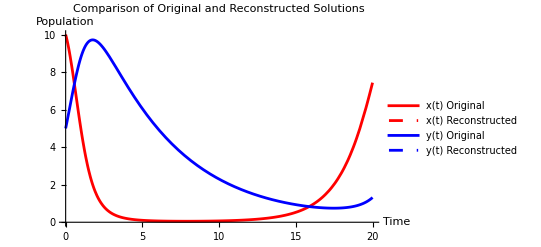
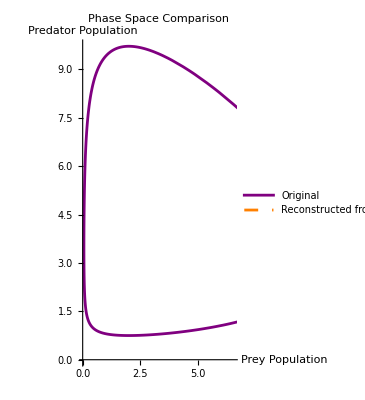
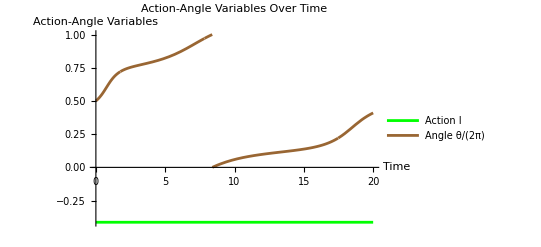

Action variable: I = -0.1 x-0.2 y+0.2 Log[x]+0.7 Log[y]

FindRoot::eqlist: In the first argument ArcTan[«1»]==0.185348&&t>5 only some of the components are equations.

ReplaceAll::reps: {FindRoot[angle[t]==angle[0]&&t>5,{t,10,5,20}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Angle variable equation of motion: dθ/dt = (2 π)/(t/.FindRoot[angle[t]==angle[0]&&t>5,{t,10,5,20}])

Solution for angle variable: θ(t) = θ0 + ωt (mod 2π)

Reconstructing x,y from I,θ requires numerical mapping along the orbit

```mathematica
(*Parameters for the Lotka-Volterra model*)α=0.7;  (*Growth rate of prey*)
β=0.2;  (*Predation rate coefficient*)
γ=0.2;  (*Death rate of predators*)
δ=0.1;  (*Reproduction rate of predators per prey eaten*)

(*Original Lotka-Volterra differential equations*)
lotkaVolterra={x'[t]==α*x[t]-β*x[t]*y[t],y'[t]==-γ*y[t]+δ*x[t]*y[t]};

(*Initial conditions*)
initialConditions={x[0]==10,(*Initial prey population*)y[0]==5    (*Initial predator population*)};

(*Solve the differential equations*)
solution=NDSolve[Join[lotkaVolterra,initialConditions],{x,y},{t,0,50}];

(*Extract solution functions*)
xSol=x/. solution[[1]];
ySol=y/. solution[[1]];

(*Find the equilibrium point*)
equilibriumX=γ/δ;
equilibriumY=α/β;
Print["Equilibrium point: (",equilibriumX,", ",equilibriumY,")"];

(*Define the conserved quantity-this is our action variable I*)
conservedH[x_,y_]:=γ*Log[x]-δ*x+α*Log[y]-β*y;

(*Calculate initial value of action variable I*)
I0=conservedH[xSol[0],ySol[0]];
Print["Initial value of action variable I = ",I0];

(*Compute period of oscillation for our orbit*)
(*First calculate angle around equilibrium*)
angle[t_]:=ArcTan[xSol[t]-equilibriumX,ySol[t]-equilibriumY];

(*Find when angle completes a full cycle*)
(*This is a simplification-we look for when angle[t]≈angle[0] after going around*)
periodFinder=FindRoot[angle[t]==angle[0]&&t>5,{t,10,5,20}];
period=t/. periodFinder;
Print["Period of oscillation for this orbit: ",period];

(*Angular frequency ω for this action value*)
ω=2π/period;
Print["Angular frequency ω = ",ω];

(*Define angle variable θ in terms of time*)
(*θ(t)=ωt (mod 2π)*)
θ[t_]:=Mod[ω*t,2π];

(*Now we need to relate (x,y) to (I,θ)*)
(*For a fixed I (conserved quantity),collect points on the orbit*)
orbitPoints=Table[{t,xSol[t],ySol[t],θ[t]},{t,0,period,period/100}];

(*Create interpolation functions to convert from angle θ to (x,y) for fixed I*)
(*Sort points by θ to ensure proper interpolation*)
sortedOrbitPoints=SortBy[orbitPoints,#[[4]]&];
xFromθ=Interpolation[{{#[[4]],#[[2]]}}&/@sortedOrbitPoints];
yFromθ=Interpolation[{{#[[4]],#[[3]]}}&/@sortedOrbitPoints];

(*Define functions to convert from (I,θ) to (x,y)*)
(*For simplicity,we fix I to I0 and only use θ*)
xFromActionAngle[i_,θ_]:=xFromθ[θ]; (*Note:i is unused,valid only for I=I0*)
yFromActionAngle[i_,θ_]:=yFromθ[θ]; (*Note:i is unused,valid only for I=I0*)

(*Define the inverse transformation-from (x,y) to (I,θ)*)
IFromXY[x_,y_]:=conservedH[x,y];

(*θ from (x,y) requires knowing which point on the orbit we're at*)
(*We'll use the angle around equilibrium as a proxy*)
θFromXY[x_,y_]:=Mod[ArcTan[x-equilibriumX,y-equilibriumY]-ArcTan[xSol[0]-equilibriumX,ySol[0]-equilibriumY]+π,2π];

(*Test the forward and inverse transformations*)
(*Test the action-angle to x,y transformation*)
testThetas=Range[0,2π,π/4];
xyFromActionAngle=Table[{xFromActionAngle[I0,θ],yFromActionAngle[I0,θ]},{θ,testThetas}];
Print["(x,y) values for different angles (fixed action I = ",I0,")"];
Print[xyFromActionAngle];

(*Test the x,y to action-angle transformation*)
testPoints=Table[{xSol[t],ySol[t]},{t,0,period,period/4}];
actionAngleFromXY=Table[{IFromXY[x,y],θFromXY[x,y]},{x,y}=#]&/@testPoints;
Print["(I,θ) values for points on the orbit:"];
Print[actionAngleFromXY];

(*Now we can express the equation of motion in terms of the angle variable*)
(*The action-angle form of the equations are:dI/dt=0 dθ/dt=ω With solutions:I(t)=I0 (constant) θ(t)=θ0+ωt (mod 2π)*)

(*Verify this by reconstructing x(t) and y(t) from the action-angle variables*)
(*Reconstructed solution*)
xReconstructed[t_]:=xFromActionAngle[I0,θ[t]];
yReconstructed[t_]:=yFromActionAngle[I0,θ[t]];

(*Compare original and reconstructed solutions*)
comparisonPlot=Plot[{xSol[t],xReconstructed[t],ySol[t],yReconstructed[t]},{t,0,20},PlotStyle->{{Red,Solid},{Red,Dashed},{Blue,Solid},{Blue,Dashed}},PlotLegends->{"x(t) Original","x(t) Reconstructed","y(t) Original","y(t) Reconstructed"},PlotLabel->"Comparison of Original and Reconstructed Solutions",AxesLabel->{"Time","Population"}];

(*Phase space comparison*)
phaseSpaceComparison=ParametricPlot[{{xSol[t],ySol[t]},{xReconstructed[t],yReconstructed[t]}},{t,0,20},PlotStyle->{{Purple,Solid},{Orange,Dashed}},PlotLegends->{"Original","Reconstructed from Action-Angle"},AxesLabel->{"Prey Population","Predator Population"},PlotLabel->"Phase Space Comparison"];

(*Show action and angle variables over time*)
actionAnglePlot=Plot[{IFromXY[xSol[t],ySol[t]],θFromXY[xSol[t],ySol[t]]/(2π)},{t,0,20},PlotStyle->{Green,Brown},PlotLegends->{"Action I","Angle θ/(2π)"},AxesLabel->{"Time","Action-Angle Variables"},PlotLabel->"Action-Angle Variables Over Time"];

(*Display the key plots*)
Grid[{{comparisonPlot},{phaseSpaceComparison},{actionAnglePlot}}]

(*Mathematical expressions-for display purposes*)
Print["Action variable: I = ",conservedH[x,y]];
Print["Angle variable equation of motion: dθ/dt = ",ω];
Print["Solution for angle variable: θ(t) = θ0 + ωt (mod 2π)"];
Print["Reconstructing x,y from I,θ requires numerical mapping along the orbit"];
```